Badges indicate graded exercises for certification

Make a list in which the number 1000 is repeated 5 times.

Expected Output »

{1000,1000,1000,1000,1000}

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

Make a table of the values of n^3 for n from 10 to 20.

Expected Output »

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
Table[n^3, {n, 10, 20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

Make a number line plot of the first 20 squares.

Expected Output »

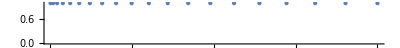

```mathematica
NumberLinePlot[Table[n^2, {n, 1, 20}]]
```

-Graphics-

Make a list of the differences between n^3 and n^2 with n up to 10.

Expected Output »

{0,4,18,48,100,180,294,448,648,900}

```mathematica
Table[n^3 - n^2, {n, 1, 10}]
```

{0,4,18,48,100,180,294,448,648,900}

Make a list of the even numbers (2, 4, 6, …) up to 20.

Expected Output »

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[2 * n, {n, 1, 10}]
```

{2,4,6,8,10,12,14,16,18,20}

Make a list of the odd numbers (1, 3, 5, …) up to 100.

Expected Output »

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
Select[Range[1, 100], OddQ]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

Make a list of the squares of even numbers up to 100.

Expected Output »

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

```mathematica
Table[n^2, {n, 0, 100, 2}]
```

{0,4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

Create the list {-3,-2,-1,0,1,2} using Range.

Expected Output »

{-3,-2,-1,0,1,2}

```mathematica
Range[-3, 2]
```

{-3,-2,-1,0,1,2}

Use Table to get the same result as

Range[10]

Expected Output »

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[i, {i, 0, 9}]
```

{0,1,2,3,4,5,6,7,8,9}

Make a bar chart of the first 10 squares.

Expected Output »

-Graphics-

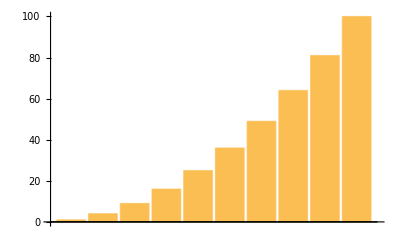

```mathematica
BarChart[Table[i^2, {i, 1, 10}]]
```

Make a list for numbers n up to 20 in which each element is a column of the values of n, n^2 and n^3.

Expected Output »

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

```mathematica
Column[Table[{n, n^2, n^3}, {n, 1, 20}]]
```

{1,1,1}
{2,4,8}
{3,9,27}
{4,16,64}
{5,25,125}
{6,36,216}
{7,49,343}
{8,64,512}
{9,81,729}
{10,100,1000}
{11,121,1331}
{12,144,1728}
{13,169,2197}
{14,196,2744}
{15,225,3375}
{16,256,4096}
{17,289,4913}
{18,324,5832}
{19,361,6859}
{20,400,8000}

Make a table of lists of digits for the first 10 squares.

Expected Output »

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

```mathematica
Table[IntegerDigits[n^2], {n, 1, 10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

Make a list line plot of the length of the sequence of digits for each of the first 100 squares.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]], {n, 1, 100}]]
```

-Graphics-

Make a table of the first digits of the first 20 squares.

Expected Output »

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

Table[IntegerDigits[n^2][[1]], {n, 1, 20}]

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

Make a list line plot of the first digits of the first 100 squares.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Table[IntegerDigits[n^2][[1]], {n, 1, 100}]]
```

-Graphics-

Make a list line plot of the last digit of each of the first 100 squares.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Mod[Range[100]^2, 10]]
```

-Graphics-

-Graphics-

Make a list line plot of the first digit of the first 100 multiples of 3.

Expected Output »

-Graphics-

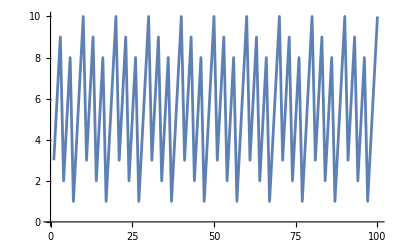

```mathematica
ListLinePlot[Mod[Range[3, 300, 3], 10] /. {0 -> 10}]
```

```mathematica
1
```

Make a list line plot of the total of the digits for each number up to 200.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Total /@ IntegerDigits[Range[200]]]
```

-Graphics-

Make a list line plot of the total of the digits for each of the first 100 squares.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Total /@ IntegerDigits[Range[100]^2]]
```

-Graphics-

Make a number line plot of the numbers 1/n with n from 1 to 20.

Expected Output »

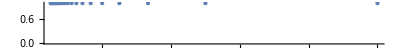

```mathematica
NumberLinePlot[Table[1/n, {n, 1, 20}]]
```

-Graphics-

Make a line plot of a list of 100 random integers where the n^th integer is between 0 and n.

Expected Output »

-Graphics-

```mathematica
ListLinePlot[Table[RandomInteger[{0, n}], {n, 1, 100}]]
```

-Graphics-